# CIFAR-100 CLASSIFICATION USING 3 INDUCTIVE LEARNING ALGORITHMS

## Name: Shilpashree Rao, USC ID: 5636765972, Email-id: shilpasr@usc.edu

### CIFAR-100 Dataset: The CIFAR-100 dataset consists of 60000 32x32 colour images in 100 classes, with 600 images per class. There are 50000 training images and 10000 test images. There are 500 training images and 100 testing images per class. The 100 classes in the CIFAR-100 are grouped into 20 superclasses. Each image comes with a “fine” label (the class to which it belongs) and a “coarse” label (the superclass to which it belongs).

### Problem Statement and Implementation: The supervised/ inductive learning algorithms such as the Convolutional Neural Network, Decision tree and k-Nearest Neighbors are used classify the 50,000 images into 100 possible categories. Holdout cross validation is implemented where in the CIFAR-100 dataset is partitioned as the training and testing datasets. Learning happens using the training samples and it is tested using the testing samples. The algorithms should train the system without over-fitting to achieve some of the performance goals such as speed and accuracy. Image properties should be considered to choose the right pre-processing algorithms to suitably feed into the learning system. The learning is done using Feed Forward Neural Network, Random Forest Decision tree and k-Nearest Neighbors algorithms here.

### Reading Data and Pre-processing: The training and testing data are read from the CIFAR-100 database and are pre-processed using ‘Image Adjust’ function. This function adjusts the levels in image, rescaling them to cover the range 0 to 1, i.e., contrast of the image is stretched over the range 0 to 255 pixels and rescaled to fall between 0 and 1. The performance of this function alone was found to better than the following pre-processing experiments for all the algorithms: 1. Raw Data 2. Image Adjust + Fourier Discrete Cosine Transformation 3. Image Adjust + Resize image to half the size + Remove Background + Gabor filter 4. Image Adjust + Resize image to half the size 5. Image Adjust + Grayscale 6. Image Adjust + Resize + Standardize

### Setting up the data: After pre-processing the images, 25,000 images are extracted from the training dataset out of 50,000 images. This is done by choosing alternate images from the training data, thus extracting 250 images per class. The testing samples are randomly selected from 10,000 images to create a subset of 5,000 images. This preserves the ratio, training set : testing set of 5 : 1. Each learning algorithm takes about 3-4 hours for computation for all the 50,000 images. By taking a subset of the dataset, the computation time for this entire notebook is reduced to 5-6 hours. However, the accuracy of the algorithms are reduced. Thus, as the learning system is trained with more and more samples, learning is improved and test accuracy increases, when over-fitting is taken care of.

```mathematica
(*Fetching the CIFAR-100 Dataset*)
dataset = ResourceObject["CIFAR-100"] 
(*Fetching the Training Data*)
trainData = ResourceData[dataset, "TrainingData"];  
 (*Fetching the Testing Dataset*)
testData = ResourceData[dataset, "TestData"]; 
(*Function to perform image adjust on the dataset*)(*adjusts the levels in image,rescaling them to cover the range 0 to 1*)
k[x_] := ImageAdjust[x];  
(*apply pre-processing to training data*)
adjImgs  = KeyMap[k, <|trainData|>]; 
 (*apply pre-processing to testing data*)
adjImgstes  = KeyMap[k, <|testData|>];
(*convert images to list form*)
a = Normal[adjImgs];  
(*creating training dataset subset of 25,000 images*)
b = a[[1 ;; Length[a] ;; 2]]; 
c = a[[2 ;; Length[a] ;; 2]];
d  = RandomSample[c, 7]; 
trainInput = Join[b, d];  
(*creating testing dataset subset of  images*)
testInput = RandomSample[Normal[adjImgstes], 5000];
```

ResourceObject[…]

### Example:

```mathematica
(*sample raw train data*)
```

```mathematica
ex = RandomSample[<|trainData|>, 1]
```

<|-Graphics-→aquarium fish|>

```mathematica
h[y_] := ImageHistogram[y];
```

```mathematica
(*histogram of the raw train data*)
```

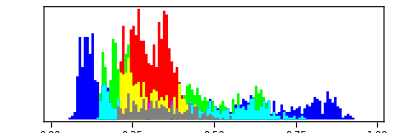
<|-Graphics-→aquarium fish|>

```mathematica
historig  = KeyMap[h, ex]
```

```mathematica
(*sample image after pre-processing*)
```

```mathematica
adjex  = KeyMap[k, ex]
```

<|-Graphics-→aquarium fish|>

```mathematica
(*histogram of the image adjusted train data - The pixel values of the image is stretched between 0 and 1*)
```

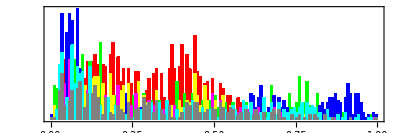
<|-Graphics-→aquarium fish|>

```mathematica
histex = KeyMap[h, adjex]
```

## CONVOLUTION NEURAL NETWORK

### Classification: The experiments were performed on LENET and Multilayer Feed-Forward Network. The performance of latter was better, and thus has been implemented below. The hidden nodes in the network, expands the scope of the possible functions the network can utilize to classify the data. Pre-determination of the number of layers and hidden nodes is not possible.

```mathematica
(*Implementation of Feed Forward Network with improved Performance Goal parameter*)
```

```mathematica
net = Classify[trainInput, Method->"NeuralNetwork", PerformanceGoal->"TrainingSpeed"]
(*compute measuremnts of the network*)
measurements1 = ClassifierMeasurements[net, testInput]
ClassifierInformation[net]
```

ClassifierFunction[…]

ClassifierMeasurementsObject[…]

Classifier information
Method | Neural network
Number of classes | 100
Number of features | 1
Number of training examples | 25000
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,382382
Hidden layer activation functions | ,,Rectified LinearRectified Linear
CostFunction | Cost Function

### Results and Visualizations:

0.5854

{{29,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,8,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0},{0,45,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0,0},{0,0,28,0,0,0,0,0,0,0,0,3,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,6,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0},{0,0,0,12,3,0,0,1,0,0,0,0,0,0,1,3,0,0,0,4,0,5,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,4,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,4,0,0,2,0,1,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},93,{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,2,0,0,0,2,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,32,0,0,0},{0,0,7,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,0,0,0,0,0,0,0,1,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,39,0}}
 |  |  |  |

<|apple→0.690476,aquarium fish→0.789474,baby→0.583333,bear→0.230769,beaver→0.25,bed→0.54717,bee→0.754386,beetle→0.55814,bicycle→0.666667,bottle→0.754717,bowl→0.369565,boy→0.178571,bridge→0.555556,bus→0.480769,butterfly→0.6875,camel→0.603774,can→0.8,castle→0.826923,caterpillar→0.824561,cattle→0.46,chair→0.814815,chimpanzee→0.74,clock→0.6875,cloud→0.653846,cockroach→0.717391,computer keyboard→0.9,couch→0.340426,crab→0.44898,crocodile→0.23913,cup→0.782609,dinosaur→0.603774,dolphin→0.612245,elephant→0.466667,flatfish→0.509804,forest→0.45098,fox→0.528302,girl→0.22,hamster→0.735849,house→0.557692,kangaroo→0.588235,lamp→0.5,lawn-mower→0.666667,leopard→0.641509,lion→0.508772,lizard→0.531915,lobster→0.529412,man→0.404255,maple tree→0.313725,motorcycle→0.781818,mountain→0.586957,mouse→0.294118,mushroom→0.633333,oak tree→0.666667,orange→0.825,orchid→0.886792,otter→0.0714286,palm tree→0.736842,pear→0.625,pickup truck→0.701754,pine tree→0.442308,plain→0.607843,plate→0.729167,poppy→0.807692,porcupine→0.595238,possum→0.294118,rabbit→0.306122,raccoon→0.410714,ray→0.418605,road→0.672727,rocket→0.425532,rose→0.622642,sea→0.790698,seal→0.372549,shark→0.62,shrew→0.311111,skunk→0.730769,skyscraper→0.82,snail→0.693878,snake→0.660377,spider→0.627119,squirrel→0.4375,streetcar→0.54,sunflower→0.857143,sweet pepper→0.638298,table→0.577778,tank→0.682927,telephone→0.75,television→0.738095,tiger→0.612245,tractor→0.87234,train→0.519231,trout→0.854167,tulip→0.470588,turtle→0.596154,wardrobe→0.846154,whale→0.346154,willow tree→0.369565,wolf→0.64,woman→0.222222,worm→0.722222|>

<|apple→0.878788,aquarium fish→0.789474,baby→0.424242,bear→0.705882,beaver→0.393939,bed→0.630435,bee→0.68254,beetle→0.533333,bicycle→0.918919,bottle→0.784314,bowl→0.472222,boy→0.3125,bridge→0.384615,bus→0.581395,butterfly→0.66,camel→0.561404,can→0.689655,castle→0.589041,caterpillar→0.534091,cattle→0.425926,chair→0.897959,chimpanzee→0.578125,clock→0.75,cloud→0.73913,cockroach→0.767442,computer keyboard→0.818182,couch→0.551724,crab→0.846154,crocodile→0.6875,cup→0.666667,dinosaur→0.711111,dolphin→0.666667,elephant→0.7,flatfish→0.4,forest→0.359375,fox→0.682927,girl→0.203704,hamster→0.735849,house→0.508772,kangaroo→0.5,lamp→0.72973,lawn-mower→0.909091,leopard→0.523077,lion→0.604167,lizard→0.471698,lobster→0.380282,man→0.339286,maple tree→0.8,motorcycle→0.895833,mountain→0.642857,mouse→0.652174,mushroom→0.716981,oak tree→0.473684,orange→0.916667,orchid→0.602564,otter→0.136364,palm tree→0.823529,pear→0.9375,pickup truck→0.727273,pine tree→0.370968,plain→0.861111,plate→0.648148,poppy→0.763636,porcupine→0.446429,possum→0.6,rabbit→0.576923,raccoon→0.821429,ray→0.580645,road→0.860465,rocket→0.714286,rose→0.647059,sea→0.548387,seal→0.279412,shark→0.516667,shrew→0.538462,skunk→0.584615,skyscraper→0.561644,snail→0.459459,snake→0.686275,spider→0.804348,squirrel→0.33871,streetcar→0.613636,sunflower→0.807692,sweet pepper→0.555556,table→0.4,tank→0.41791,telephone→0.557143,television→0.584906,tiger→0.535714,tractor→0.532468,train→0.6,trout→0.471264,tulip→0.648649,turtle→0.424658,wardrobe→0.709677,whale→0.818182,willow tree→0.369565,wolf→0.410256,woman→0.217391,worm→0.722222|>

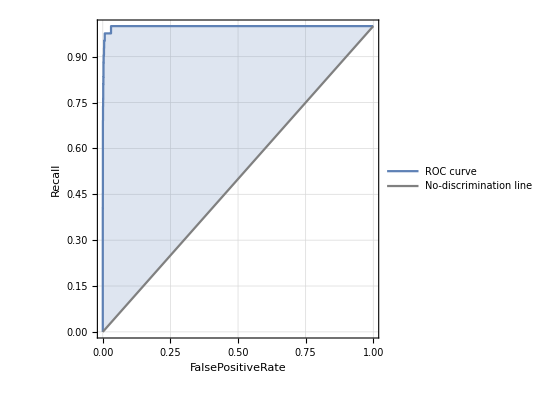
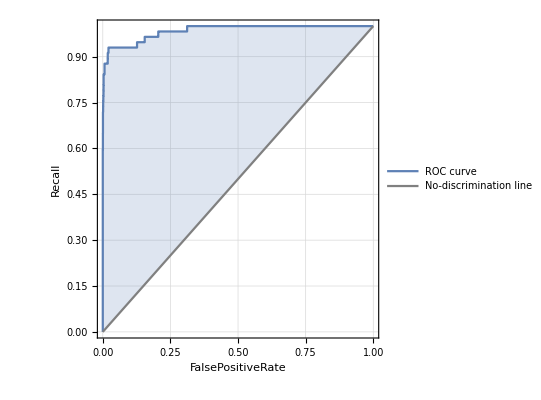
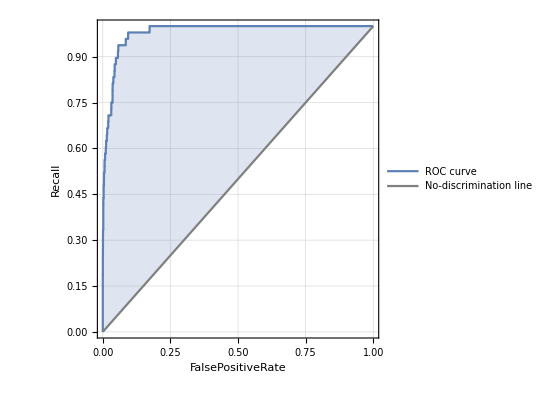
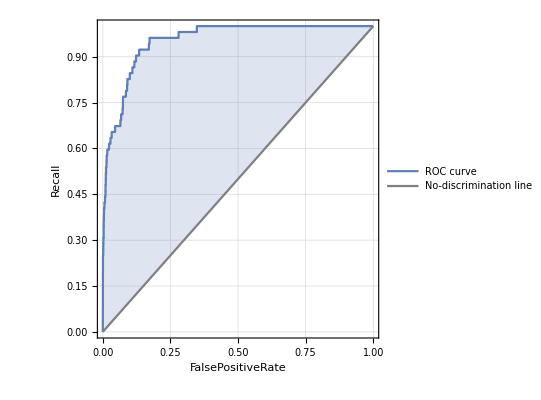
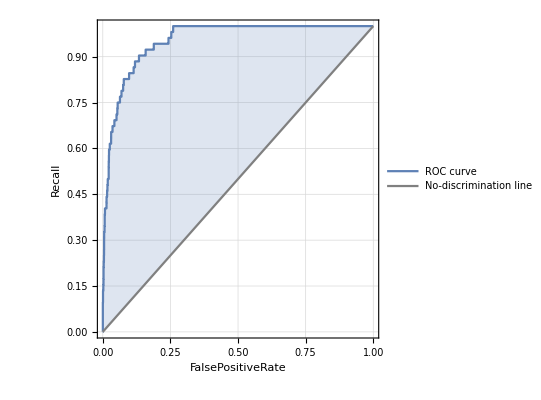
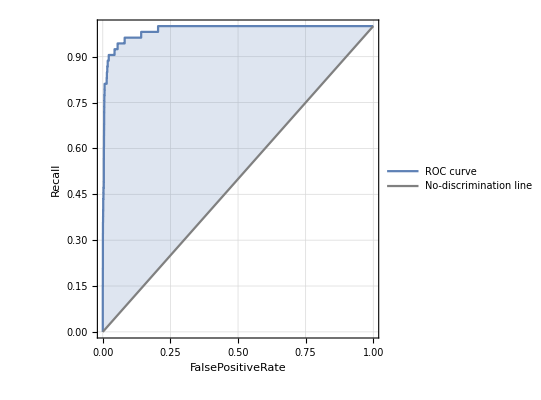
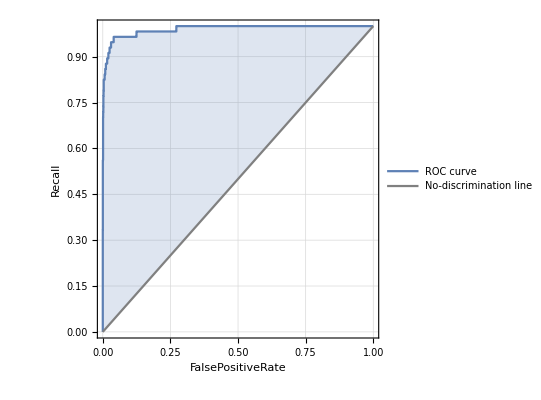
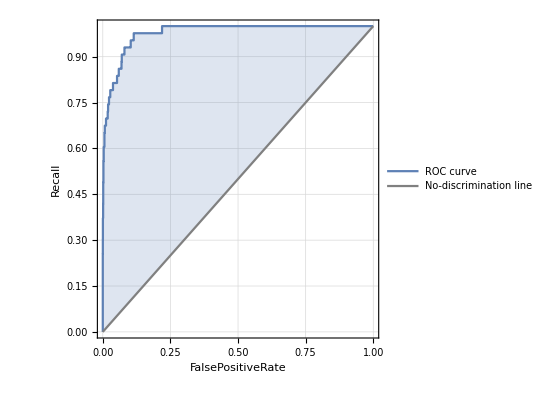
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,«80»,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
measurements1["Accuracy"]
measurements1["ConfusionMatrix"]
measurements1["Recall"]
measurements1["Precision"]
Short[measurements1["ROCCurve"]]
```

```mathematica
measurements1["BestClassifiedExamples"]
```

{-Graphics-→computer keyboard,-Graphics-→computer keyboard,-Graphics-→computer keyboard,-Graphics-→computer keyboard,-Graphics-→wolf,-Graphics-→cup,-Graphics-→cup,-Graphics-→computer keyboard,-Graphics-→computer keyboard,-Graphics-→orchid}

```mathematica
measurements1["WorstClassifiedExamples"]
```

{-Graphics-→pear,-Graphics-→camel,-Graphics-→elephant,-Graphics-→forest,-Graphics-→mountain,-Graphics-→table,-Graphics-→tulip,-Graphics-→lizard,-Graphics-→shrew,-Graphics-→rabbit}

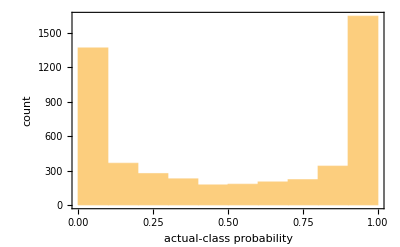

```mathematica
measurements1["ProbabilityHistogram"]
```

## DECISION TREE: RANDOM FOREST

### Classification: This algorithm was chosen as the depth of the tree can be optimized to avoid over-fitting or fit noise in the data

```mathematica
(*Implementation of Random Forest with improved Performance Goal and Variable sample size parameters*)
```

```mathematica
rfClassifier = Classify[trainInput,Method->{"RandomForest","VariableSampleSize"-> 5, PerformanceGoal->"TrainingSpeed"}]
(*compute measuremnts of the decision tree*)
measurements2 = ClassifierMeasurements[rfClassifier, testInput]
ClassifierInformation[rfClassifier]
```

ClassifierFunction[…]

ClassifierMeasurementsObject[…]

Classifier information
Method | Random forest
Number of classes | 100
Number of features | 1
Number of training examples | 25000
Number of trees | 50

### Results and Visualizations:

0.445

{{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,51,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},97,{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,3,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,36,0}}
 |  |  |  |

<|apple→0.952381,aquarium fish→0.894737,baby→0.520833,bear→0.192308,beaver→0.0384615,bed→0.471698,bee→0.45614,beetle→0.44186,bicycle→0.764706,bottle→0.773585,bowl→0.23913,boy→0.125,bridge→0.222222,bus→0.596154,butterfly→0.541667,camel→0.0377358,can→0.56,castle→0.807692,caterpillar→0.561404,cattle→0.42,chair→0.87037,chimpanzee→0.58,clock→0.5625,cloud→0.75,cockroach→0.73913,computer keyboard→0.925,couch→0.0212766,crab→0.163265,crocodile→0.173913,cup→0.804348,dinosaur→0.45283,dolphin→0.591837,elephant→0.288889,flatfish→0.137255,forest→0.470588,fox→0.603774,girl→0.,hamster→0.867925,house→0.211538,kangaroo→0.333333,lamp→0.444444,lawn-mower→0.7,leopard→0.320755,lion→0.719298,lizard→0.0851064,lobster→0.,man→0.106383,maple tree→0.54902,motorcycle→0.8,mountain→0.543478,mouse→0.,mushroom→0.15,oak tree→0.796296,orange→0.925,orchid→0.867925,otter→0.0238095,palm tree→0.684211,pear→0.583333,pickup truck→0.736842,pine tree→0.153846,plain→0.784314,plate→0.6875,poppy→0.807692,porcupine→0.142857,possum→0.196078,rabbit→0.,raccoon→0.339286,ray→0.,road→0.763636,rocket→0.489362,rose→0.660377,sea→0.581395,seal→0.137255,shark→0.58,shrew→0.0666667,skunk→0.576923,skyscraper→0.58,snail→0.44898,snake→0.641509,spider→0.254237,squirrel→0.,streetcar→0.26,sunflower→0.897959,sweet pepper→0.276596,table→0.0666667,tank→0.341463,telephone→0.673077,television→0.785714,tiger→0.163265,tractor→0.191489,train→0.0192308,trout→0.479167,tulip→0.196078,turtle→0.153846,wardrobe→0.653846,whale→0.442308,willow tree→0.0217391,wolf→0.36,woman→0.355556,worm→0.666667|>

<|apple→0.487805,aquarium fish→0.383459,baby→0.403226,bear→0.136986,beaver→0.285714,bed→0.316456,bee→0.464286,beetle→0.301587,bicycle→0.371429,bottle→0.356522,bowl→0.5,boy→0.2,bridge→0.444444,bus→0.348315,butterfly→0.371429,camel→0.666667,can→0.54902,castle→0.488372,caterpillar→0.367816,cattle→0.333333,chair→0.443396,chimpanzee→0.358025,clock→0.529412,cloud→0.402062,cockroach→0.333333,computer keyboard→0.381443,couch→0.2,crab→0.571429,crocodile→0.615385,cup→0.486842,dinosaur→0.307692,dolphin→0.42029,elephant→0.393939,flatfish→0.7,forest→0.421053,fox→0.410256,girl→0.,hamster→0.308725,house→0.366667,kangaroo→0.369565,lamp→0.571429,lawn-mower→0.538462,leopard→0.425,lion→0.344538,lizard→0.4,lobster→Indeterminate,man→0.3125,maple tree→0.474576,motorcycle→0.556962,mountain→0.378788,mouse→0.,mushroom→0.9,oak tree→0.387387,orange→0.560606,orchid→0.469388,otter→0.333333,palm tree→0.443182,pear→0.444444,pickup truck→0.446809,pine tree→0.615385,plain→0.615385,plate→0.445946,poppy→0.531646,porcupine→0.461538,possum→0.232558,rabbit→0.,raccoon→0.612903,ray→0.,road→0.552632,rocket→0.560976,rose→0.583333,sea→0.625,seal→0.411765,shark→0.467742,shrew→0.428571,skunk→0.491803,skyscraper→0.604167,snail→0.468085,snake→0.507463,spider→0.681818,squirrel→0.,streetcar→0.541667,sunflower→0.676923,sweet pepper→0.52,table→0.428571,tank→0.636364,telephone→0.673077,television→0.568966,tiger→0.727273,tractor→0.692308,train→1.,trout→0.638889,tulip→0.666667,turtle→0.888889,wardrobe→0.641509,whale→0.534884,willow tree→0.125,wolf→0.62069,woman→0.222222,worm→0.765957|>

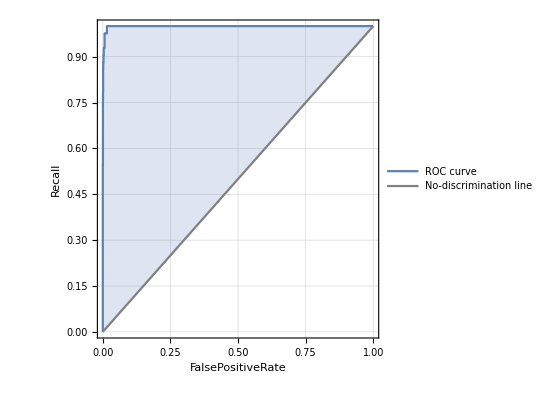
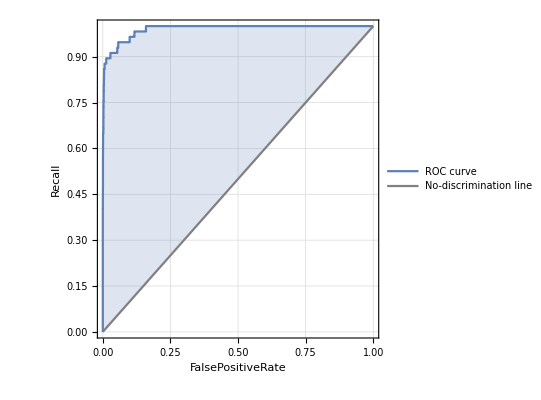
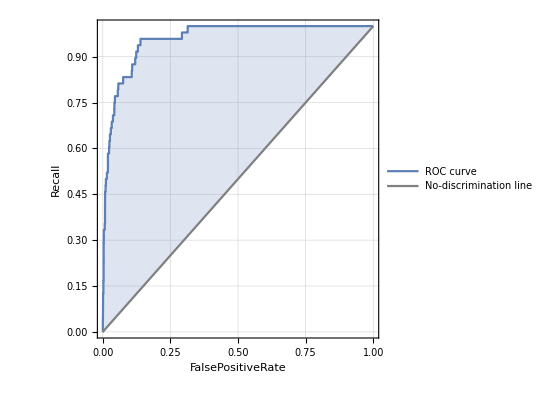
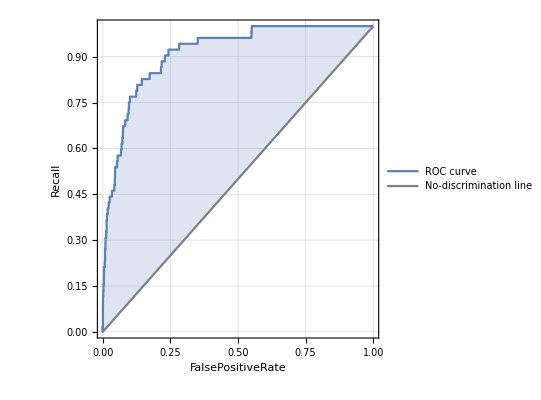
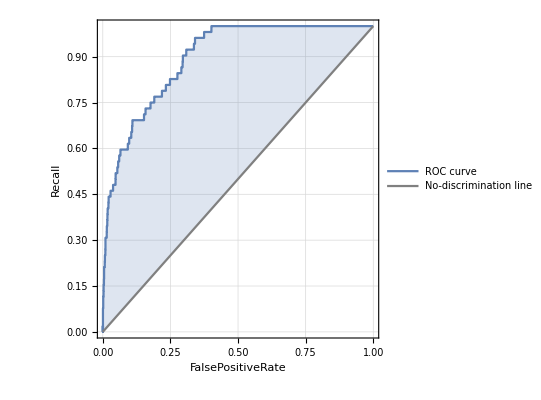
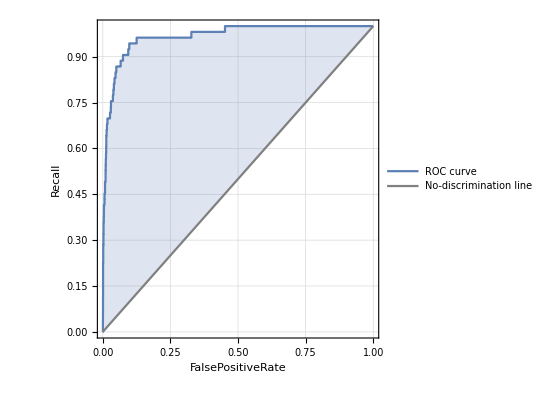
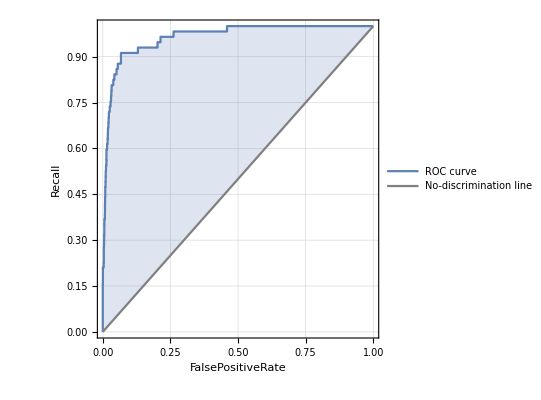
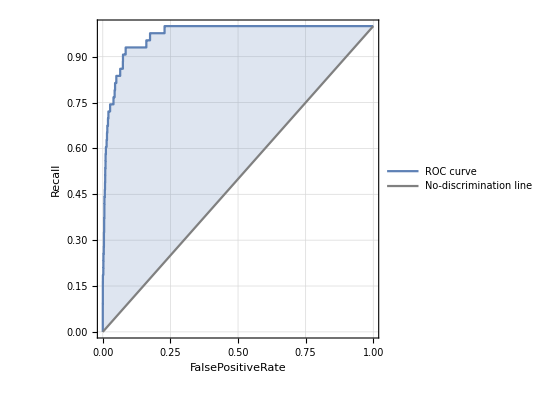
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,«80»,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
measurements2["Accuracy"]
measurements2["ConfusionMatrix"]
measurements2["Recall"]
measurements2["Precision"]
Short[measurements2["ROCCurve"]]
```

```mathematica
measurements2["BestClassifiedExamples"]
```

{-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower,-Graphics-→sunflower}

```mathematica
measurements2["WorstClassifiedExamples"]
```

{-Graphics-→cockroach,-Graphics-→can,-Graphics-→palm tree,-Graphics-→poppy,-Graphics-→rocket,-Graphics-→rocket,-Graphics-→chair,-Graphics-→rose,-Graphics-→plain,-Graphics-→mountain}

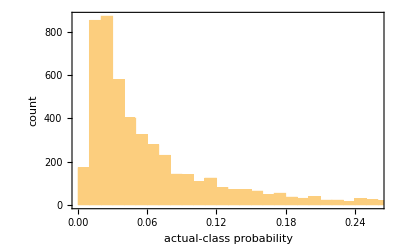

```mathematica
measurements2["ProbabilityHistogram"]
```

## MACHINE LEARNING ALGORITHM: k- NEAREST NEIGHBORS

### Classification: This algorithm was chosen as there is freedom to play around with the Number of Neighbors parameter for performance optimization

```mathematica
(*Implementation of k-Nearest Neighbors with improved Performance Goal and Number of Neighbors parameters*)
```

```mathematica
nnClassifier = Classify[trainInput,Method->{"NearestNeighbors", "NeighborsNumber"-> 10,  PerformanceGoal-> "TrainingSpeed"}]
(*compute measuremnts of ML algorithm*)
measurements3 = ClassifierMeasurements[nnClassifier, testInput]
ClassifierInformation[nnClassifier]
```

ClassifierFunction[…]

ClassifierMeasurementsObject[…]

Classifier information
Method | K-nearest neighbors
Number of classes | 100
Number of features | 1
Number of training examples | 25000
Number of neighbors | 10
Distance function | EuclideanDistance

### Results and Visualizations:

0.5498

{{41,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,50,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},97,{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,42,0}}
 |  |  |  |

<|apple→0.97619,aquarium fish→0.877193,baby→0.416667,bear→0.25,beaver→0.269231,bed→0.509434,bee→0.561404,beetle→0.465116,bicycle→0.686275,bottle→0.773585,bowl→0.23913,boy→0.196429,bridge→0.361111,bus→0.519231,butterfly→0.395833,camel→0.283019,can→0.68,castle→0.769231,caterpillar→0.526316,cattle→0.32,chair→0.703704,chimpanzee→0.72,clock→0.541667,cloud→0.730769,cockroach→0.695652,computer keyboard→0.9,couch→0.404255,crab→0.44898,crocodile→0.456522,cup→0.73913,dinosaur→0.433962,dolphin→0.489796,elephant→0.511111,flatfish→0.372549,forest→0.45098,fox→0.528302,girl→0.32,hamster→0.754717,house→0.596154,kangaroo→0.431373,lamp→0.481481,lawn-mower→0.65,leopard→0.45283,lion→0.614035,lizard→0.361702,lobster→0.352941,man→0.617021,maple tree→0.568627,motorcycle→0.763636,mountain→0.608696,mouse→0.352941,mushroom→0.45,oak tree→0.648148,orange→0.9,orchid→0.849057,otter→0.214286,palm tree→0.666667,pear→0.604167,pickup truck→0.789474,pine tree→0.5,plain→0.803922,plate→0.6875,poppy→0.75,porcupine→0.47619,possum→0.235294,rabbit→0.265306,raccoon→0.339286,ray→0.418605,road→0.745455,rocket→0.659574,rose→0.811321,sea→0.604651,seal→0.431373,shark→0.52,shrew→0.244444,skunk→0.557692,skyscraper→0.76,snail→0.632653,snake→0.584906,spider→0.644068,squirrel→0.291667,streetcar→0.54,sunflower→0.857143,sweet pepper→0.531915,table→0.4,tank→0.487805,telephone→0.596154,television→0.833333,tiger→0.326531,tractor→0.765957,train→0.25,trout→0.770833,tulip→0.431373,turtle→0.365385,wardrobe→0.865385,whale→0.480769,willow tree→0.434783,wolf→0.58,woman→0.355556,worm→0.777778|>

<|apple→0.683333,aquarium fish→0.793651,baby→0.47619,bear→0.295455,beaver→0.304348,bed→0.5,bee→0.780488,beetle→0.689655,bicycle→0.744681,bottle→0.803922,bowl→0.44,boy→0.354839,bridge→0.342105,bus→0.54,butterfly→0.76,camel→0.555556,can→0.809524,castle→0.57971,caterpillar→0.697674,cattle→0.551724,chair→0.883721,chimpanzee→0.642857,clock→0.928571,cloud→0.457831,cockroach→0.711111,computer keyboard→0.818182,couch→0.345455,crab→0.594595,crocodile→0.381818,cup→0.871795,dinosaur→0.657143,dolphin→0.545455,elephant→0.328571,flatfish→0.5,forest→0.205357,fox→0.518519,girl→0.290909,hamster→0.666667,house→0.462687,kangaroo→0.338462,lamp→0.742857,lawn-mower→0.866667,leopard→0.444444,lion→0.460526,lizard→0.5,lobster→0.382979,man→0.402778,maple tree→0.517857,motorcycle→0.75,mountain→0.56,mouse→0.36,mushroom→0.75,oak tree→0.492958,orange→0.734694,orchid→0.737705,otter→0.333333,palm tree→0.791667,pear→0.878788,pickup truck→0.737705,pine tree→0.448276,plain→0.640625,plate→0.611111,poppy→0.696429,porcupine→0.454545,possum→0.5,rabbit→0.52,raccoon→0.404255,ray→0.418605,road→0.577465,rocket→0.596154,rose→0.716667,sea→0.490566,seal→0.268293,shark→0.448276,shrew→0.23913,skunk→0.58,skyscraper→0.808511,snail→0.738095,snake→0.815789,spider→0.655172,squirrel→0.241379,streetcar→0.325301,sunflower→0.823529,sweet pepper→0.714286,table→0.375,tank→0.465116,telephone→0.861111,television→0.486111,tiger→0.470588,tractor→0.62069,train→0.448276,trout→0.596774,tulip→0.814815,turtle→0.655172,wardrobe→0.652174,whale→0.694444,willow tree→0.227273,wolf→0.402778,woman→0.372093,worm→0.792453|>

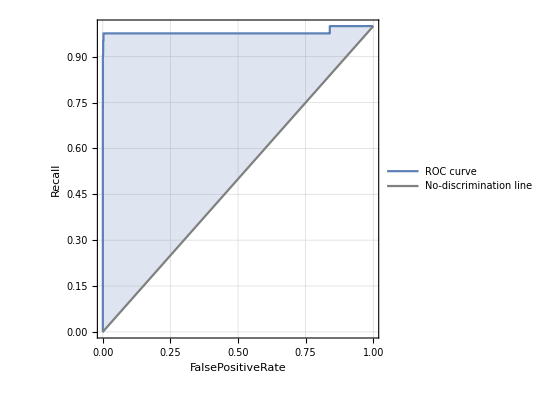
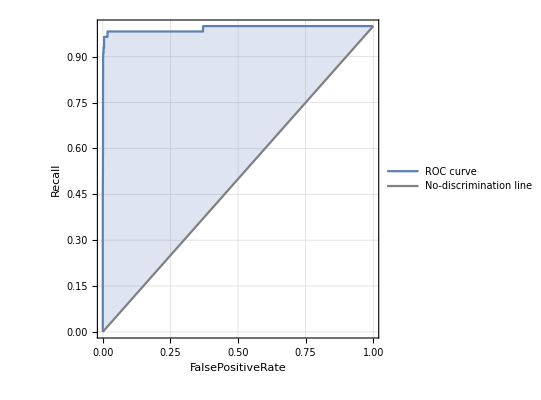
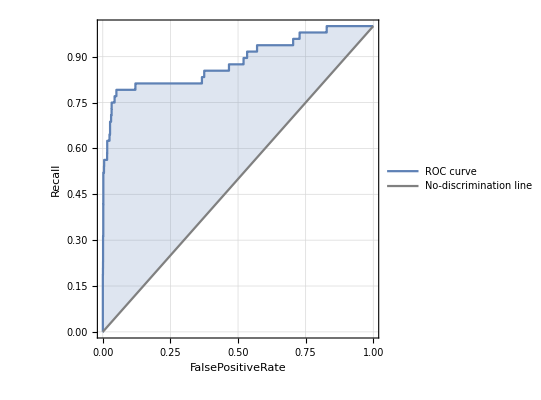
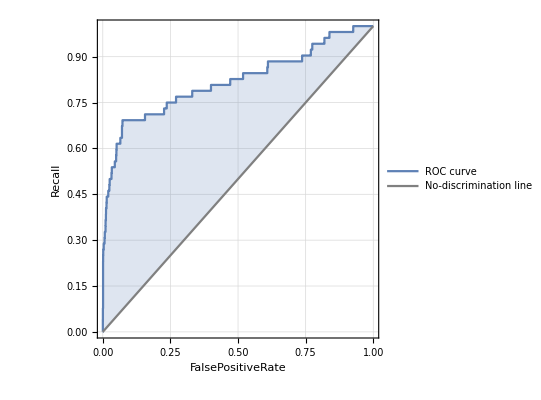
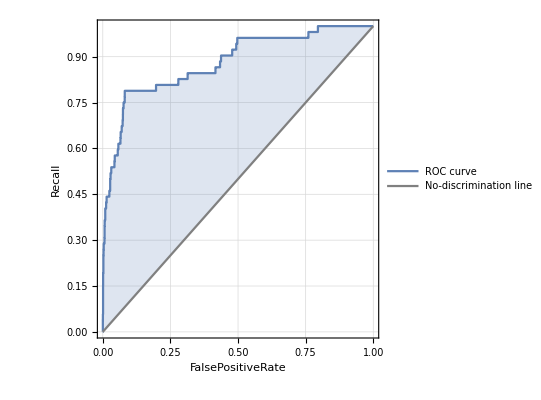
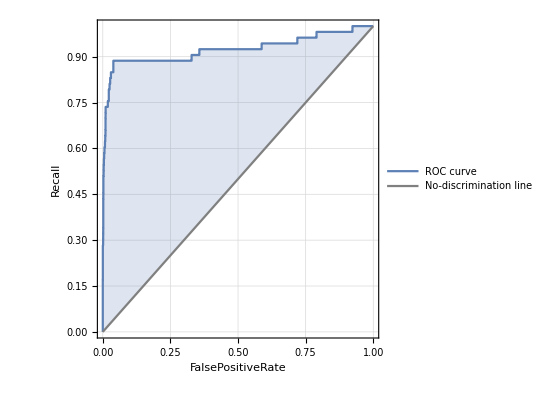
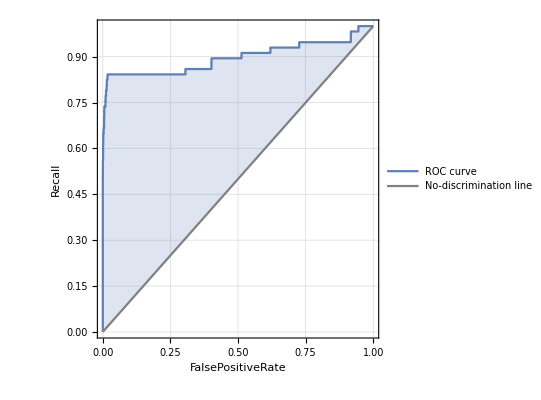
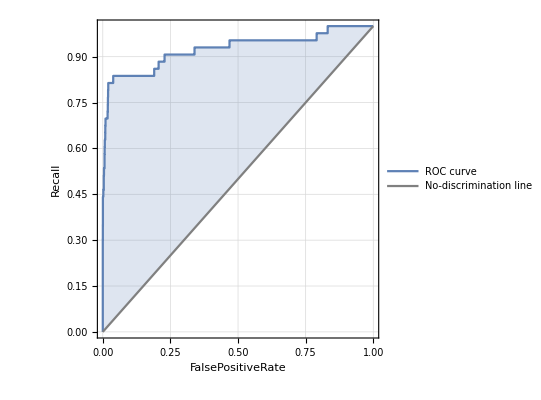
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,«80»,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
measurements3["Accuracy"]
measurements3["ConfusionMatrix"]
measurements3["Recall"]
measurements3["Precision"]
Short[measurements3["ROCCurve"]]
```

```mathematica
measurements3["BestClassifiedExamples"]
```

{-Graphics-→castle,-Graphics-→castle,-Graphics-→castle,-Graphics-→plain,-Graphics-→poppy,-Graphics-→plain,-Graphics-→plain,-Graphics-→plain,-Graphics-→plain,-Graphics-→poppy}

```mathematica
measurements3["WorstClassifiedExamples"]
```

{-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→otter,-Graphics-→aquarium fish}

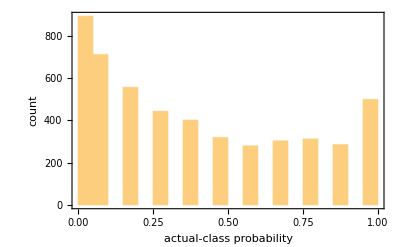

```mathematica
measurements3["ProbabilityHistogram"]
```

## Comparison of results between Convolutional Network, Random Forest and k-Nearest Neighbors Algorithms

### On applying the same pre-processing for all the algorithms, we can conclude that Neural Network performs better than k-Nearest Neighbors. Performance of the Random Forest algorithm is the poorest. The Neural Network has the advantage to calculate and manipulate it’s weights, which gives it flexibility to compute an appropriate function for classification. However, Nearest Neighbors and Random forest choose the best class from it’s neighbors and decision trees respectively. The features in the Random forest algorithm is computed randomly, thus we do not get stable results for all iterations.

## Conclusions

### • The performance of Neural Network works better than k-Nearest Neighbors for classification of CIFAR-100 • Performance of Random Forest algorithm is not as good as Neural network and k-Nearest Neighbors. The algorithm makes use of 100 trees which increases the space complexity • Nearest Neighbors can be improved further by using Hamming distance instead of Euclidean distance measurement • Pre-processing algorithms and Dimension Reduction without losing important features can be improved